```mathematica
f[x_]:= α Exp[-(x-xb)/β] x^2
D[f[x],x]/.x->xb
```

2 xb α-(xb^2 α)/β

1.5

```mathematica
ClearAll[dens]
xs = 1.0;
dens[x1_]:=(ρ0  xs^(8-3/2))/(x1^(3/2)(xs + x1)^(8-3/2))
rt = 1.5 ;
d[r_]:=r^(-3/2)*(rt^2/(r^2+rt^2))^6
```

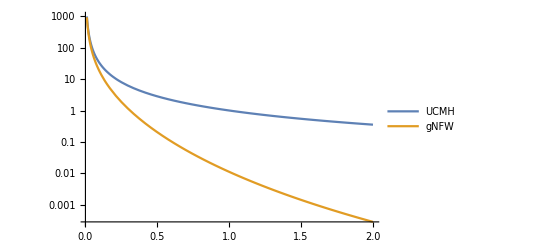

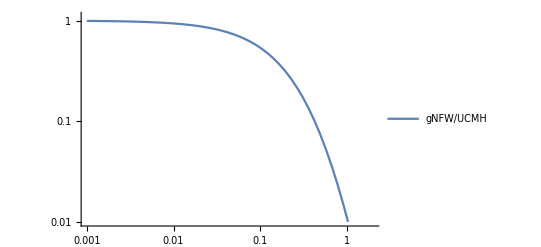

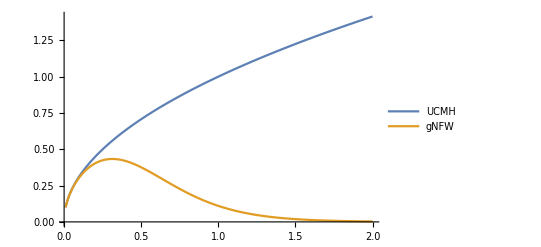

```mathematica
LogPlot[{x^(-3/2),dens[x]/ρ0},  {x, 0.01, 2}, PlotLegends->{"UCMH", "gNFW"}]
LogLogPlot[(dens[x]/ρ0)/x^(-3/2),  {x, 0.001, 2.0}, PlotLegends->{"gNFW/UCMH"}, PlotRange->{0.01,1.1}]
Plot[{x^2 x^(-3/2),x^2 d[x]},  {x, 0.01, 2}, PlotLegends->{"UCMH", "gNFW"}]
```

```mathematica
MPBH = 30.0;
rtr = 0.0063*(MPBH^(1/3));
```

```mathematica
A = 3.0*30.0/(8*π*rtr^3);
```

```mathematica
ρ[x_]:= (ρ0 x0^α)/(x^γ(x0 + x)^(α - γ))
ρ2[x_]:= (30.0(47/90)rtr^-3)/(x^(3/2)(1 + x)^(6 - 3/2))
```

```mathematica
Prad[x_] := 4 π x^2 ρ[x]
```

```mathematica
Menc[x1_] = rtr^3 FullSimplify[Assuming[{x0 > 0, γ < 3, x1 ≥ 0},Integrate[Prad[x], {x, 0, x1}]]]
1-6+3/2
```

-0.0000942655 (-1)^γ x0^3 ρ0 Beta[-x1/x0,3-γ,1-α+γ]

-7/2

```mathematica
Block[{γ = 3/2, α = 6, x0 = 1, ρ0 = 1},
Integrate[Menc[x]/x^2, {x,100,1}]]
```

-0.000013038+0. ⅈ

```mathematica
(0.+0.00009426549819026 ⅈ) (-Beta[-x,1/2,-7/2]-Beta[-x,3/2,-7/2]/x)
```

(0.+0.0000942655 ⅈ) (-Beta[-x,1/2,-7/2]-Beta[-x,3/2,-7/2]/x)

```mathematica
4π I N[Beta[-100, 3-3/2, 1-6+3/2]]
```

1.91487-3.51756×10^-16 ⅈ

```mathematica
rtr^3 Integrate[4π x^2 ρ2[x], {x, 0, 1000}]
```

29.9997

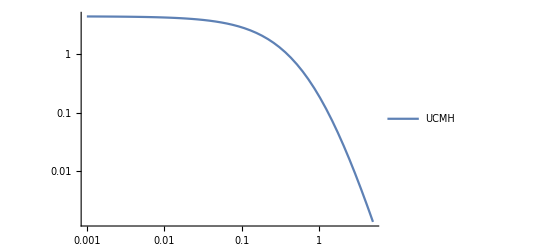

```mathematica
LogLogPlot[{ρ2[x]/(A x^(-3/2))}, {x, 10^-3, 5}, PlotLegends->{"UCMH", "gNFW"},PlotRange->All]
```

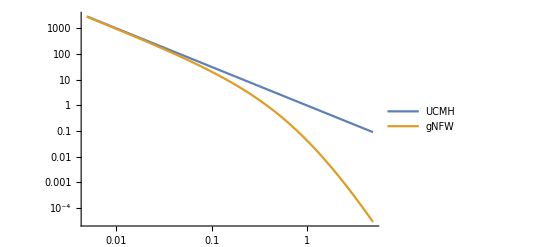

0.161283

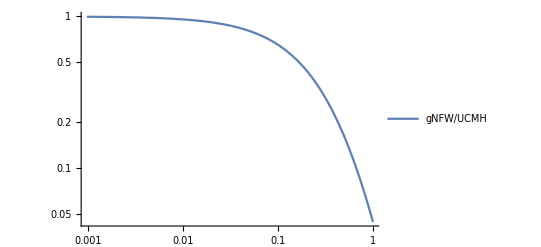

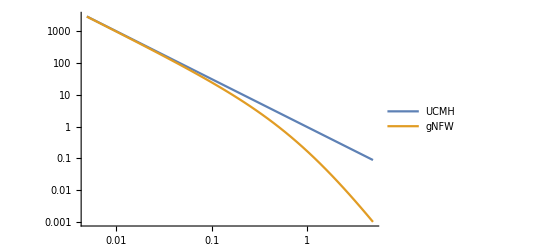

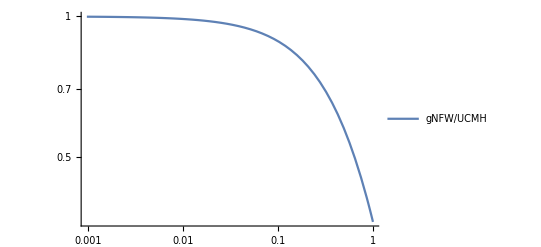

```mathematica
Block[{γ = 3/2, α = 6, x0 = 1, ρ0 = 1}, 
LogLogPlot[{ρ0 x0^γ x^(-3/2),ρ[x]}, {x, 0, 5}, PlotLegends->{"UCMH", "gNFW"}]]


Block[{γ = 3/2, α = 6, x0 = 1, ρ0 = 1},
Print[ρ[x]/(ρ0 x0^γ x^(-3/2))/.x->0.5];LogLogPlot[{ρ[x]/(ρ0 x0^γ x^(-3/2))}, {x, 0, 1}, PlotLegends->{"gNFW/UCMH"}]]
```

0.000011268-2.0699×10^-21 ⅈ

0.0000133573-2.4537×10^-21 ⅈ

0.0000139219-2.55741×10^-21 ⅈ

0.0000141326-2.59611×10^-21 ⅈ

0.0000142282-2.61368×10^-21 ⅈ

0.929901+2.46519×10^-32 ⅈ

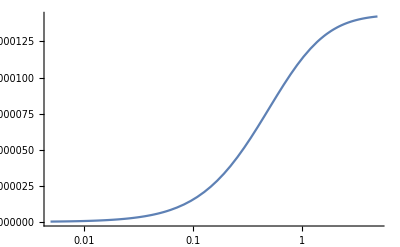

-4 (-1)^γ π x0^3 ρ0 Beta[100/x0,3-γ,1-α+γ]

-12.5664 Re[(-1.)^γ x0^3 ρ0 Beta[-10000./x0,3.-1. γ,1.-1. α+γ]]

```mathematica
Block[{γ = 3/2, α = 6, x0 = 1, ρ0 = 1}, 
Print[N[Menc[1]]];
Print[N[Menc[2]]];
Print[N[Menc[3]]];
Print[N[Menc[4]]];
Print[N[Menc[5]]];
Print[N[Menc[2]/Menc[100]]];
LogLinearPlot[Menc[x], {x, 0, 5}]]
```

```mathematica
ρfix = Block[{γ = 3/2, α = 6, x0 = 1, ρ0 = 1}, 
Print[N[Re[Menc[100000000000000000000]]]];
30/N[Re[Menc[1000]]]]
```

0.0000143643

2.08852×10^6

```mathematica
N[3/47]
```

0.0638298

```mathematica
N[90/47]
```

1.91489

```mathematica
N[47/3]
```

15.6667

45/2

1.91487-3.51756×10^-16 ⅈ

```mathematica
dens[x1_]:=((90/47) xs^(8-3/2))/(x1^(3/2)(xs + x1)^(8-3/2))
```

```mathematica
Integrate[x^2/(x^(3/2)(1+x)^(6-3/2)),{x,0, x1}]
Integrate[x^2/(x^(3/2)(1+x)^(6-3/2)),{x,0, ∞}]
```

ConditionalExpression[(2 x1^(3/2) (35+28 x1+8 x1^2))/(105 (1+x1)^(7/2)),Re[x1]>-1||x1∉Reals]

16/105

```mathematica
N[16/105]
```

0.152381

```mathematica
Assuming[{x1 > 0, y > 0},Integrate[Integrate[x^2/(x^(3/2)(1+x)^(6-3/2)),{x,0, x1}]/x1^2,{x1, y, ∞}]]
```

(2 (48-70 √(y (1+y))-112 √(y^3 (1+y))-48 √(y^5 (1+y))+48 y (3+y (3+y))))/(105 (1+y)^3)

```mathematica
ClearAll[ρ,rtr]
ρ[x_]:= ρ0/(x^(3/2)(1+x)^(6-3/2))
Menc[y_]= MPBH + 4*π*rtr^3 Integrate[ρ[x] x^2, {x, 0, y}]
```

ConditionalExpression[30.+(8 π rtr^3 y^(3/2) (35+28 y+8 y^2) ρ0)/(105 (1+y)^(7/2)),Re[y]>-1||y∉Reals]

```mathematica
ψ[x1_]= (G/rtr)Assuming[{x1 > 0},Integrate[30.0/y^2, {y, x1, ∞}]]
```

(30. G)/(rtr x1)

```mathematica
ρouter [x_]:= α Exp[-β (x-xa)]
ρouter[2]
ρinner[2]
```

ⅇ^(-(2-xa) β) α

ρ0/(162 √6)

```mathematica
6-3/2
```

9/2

```mathematica
ρinner[x_] := ρ0/(x^(3/2)(1+x)^(9/2))
FullSimplify[D[ρinner[x]/ρ0, x]]
```

-(3 (1+4 x))/(2 x^(5/2) (1+x)^(11/2))

```mathematica
Integrate[Integrate[ρouter[x] x^2, {x, 0, x1}]/x1^2, {x1, y, ∞}]
```

ConditionalExpression[-(ⅇ^((xa-y) β) α (2-2 ⅇ^(y β)+y β))/(y β^3),Re[β]>0&&Re[y]>0&&Im[y]==0]